```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
t = Import["AbsorbingBoundaryLayerScattering.mat"];
```

```mathematica
z = Flatten[t[[1]]];upsilon = Flatten[t[[2]]];potential = Flatten[t[[3]]];
```

```mathematica
upsilonFun = Interpolation[Table[{z[[i]],upsilon[[i]]},{i,1,Length[z]}]];
```

```mathematica
potentialFun = Interpolation[Table[{z[[i]],potential[[i]]},{i,1,Length[z]}]];
```

```mathematica
V[x_]:=If[x<10^-5,potentialFun[x],0];
ψ[x_]:=If[x<10^-5,upsilonFun[x],0];
```

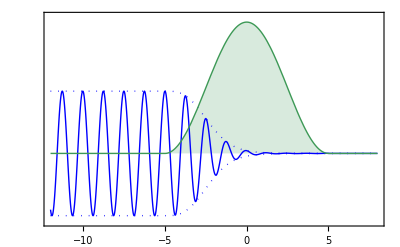

```mathematica
Plot[{Re[ψ[10^-6(x+5)]],Abs[ψ[10^-6(x+5)]],-Abs[ψ[10^-6(x+5)]],-2 10^29 Im[V[10^-6(x+5)]]},{x,-12 ,8},PlotStyle->{{Blue},{Blue,Dotted},{Blue,Dotted},Thick},Filling->{4->Axis},FrameTicks->{Automatic,None},Frame->True,PlotRangePadding->None,PlotRange->{-1.1,2.2},FrameStyle->16]
```